```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## NNLO Expansion Tests

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

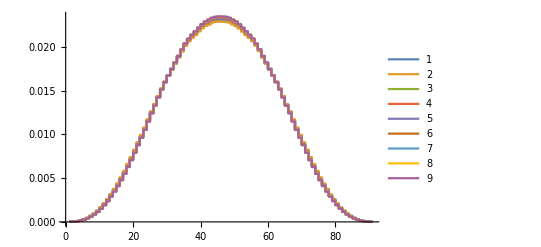

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

```mathematica
last=RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]];
```

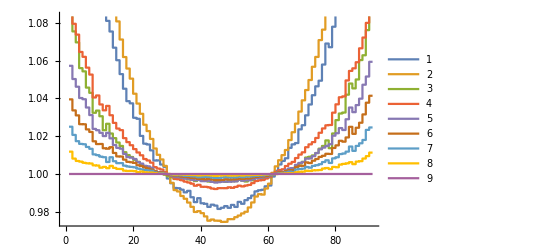

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOgg[[;;,2]]/Total[RapidityNNLOgg[[;;,2]]]/last,{i,0,8}];
ListStepPlot[%,PlotLegends->Automatic]
```

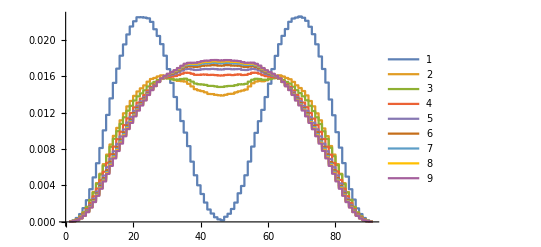

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i](RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

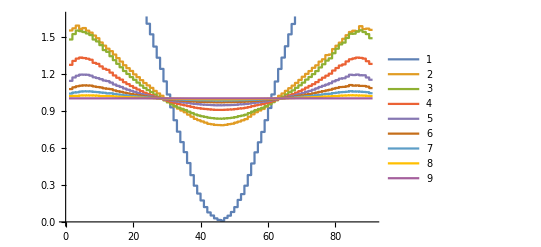

```mathematica
last=(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]];
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i](RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]])/Total[RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]]/last,{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

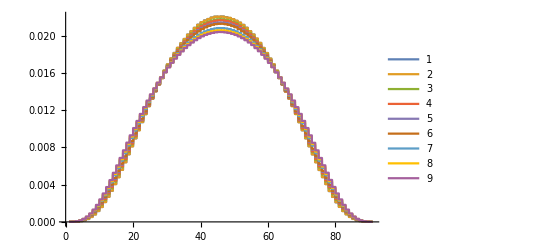

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOqqbar[[;;,2]]/Total[RapidityNNLOqqbar[[;;,2]]],{i,0,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

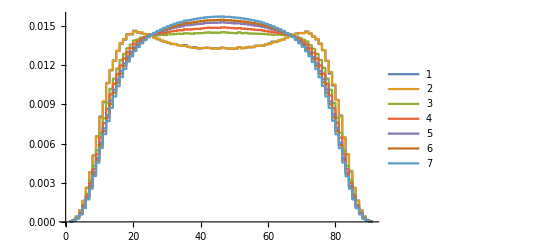

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
fac[i]RapidityNNLOqq[[;;,2]]/Total[RapidityNNLOqq[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

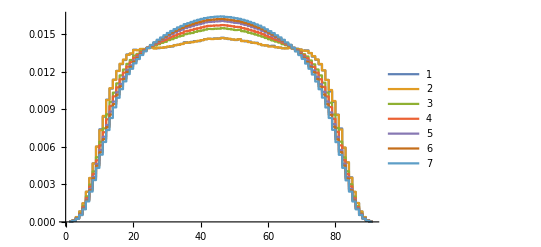

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]]/Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/._fac->1;
ListStepPlot[%,PlotLegends->Automatic]
```

## NNLO Expansion Tests with exact as a complement

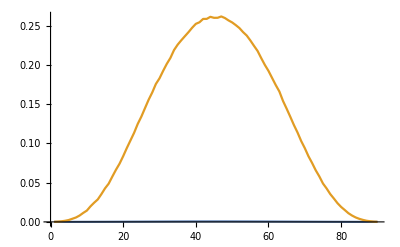

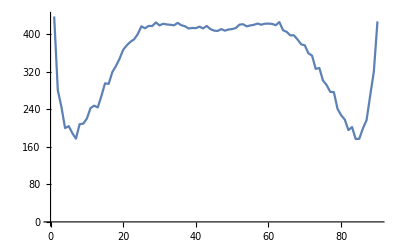

```mathematica
Get["Results/NNLOExact1.txt"]
exact=RapidityNNLOqQ2[[;;,2]];
Get["Results/NumericalNNLO.txt"]
numerical=RapidityNNLOgg[[;;,2]];
ListLinePlot[{exact,numerical}]
ListLinePlot[numerical/exact]
```

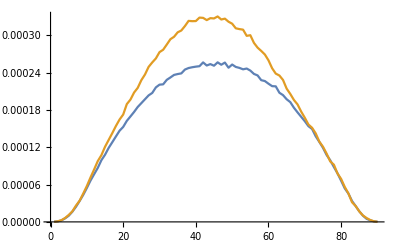

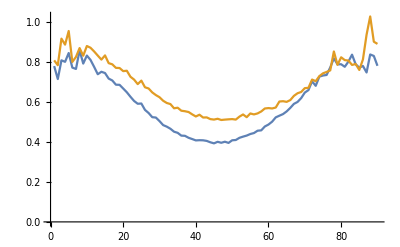

```mathematica
Get["Results/NNLOExact2.txt"]
exact2=RapidityNNLOqQ2[[;;,2]];
Get["Results/NNLOExact3.txt"]
exact3=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[{exact2,exact3}]
ListLinePlot[{exact2/exact,exact3/exact}]
```

{0.00224539,0.00521604,0.00772705,0.00948283,0.0106268,0.0113691,0.0119371}

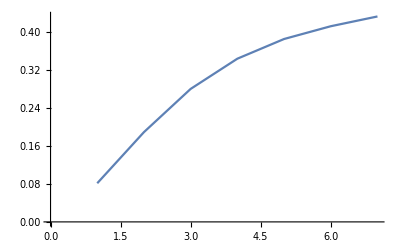

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1
ListLinePlot[%/Total[exact]]
```

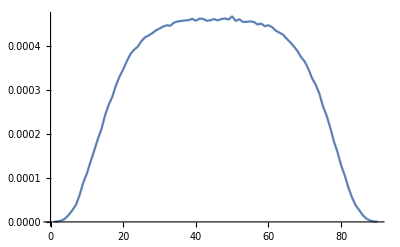

```mathematica
Get["Results/InclusiveNNLOqQ2.txt"];
IncRap=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[IncRap]
```

{200.23,199.191,199.993,199.975,199.904,199.919,199.977}

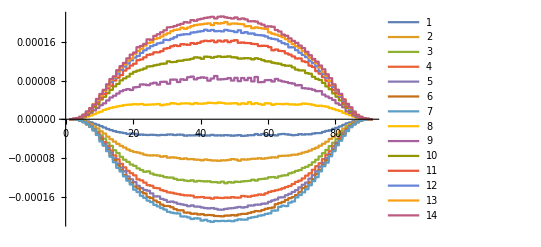

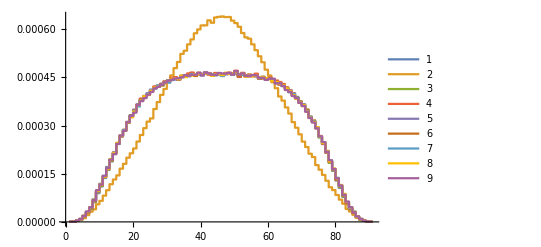

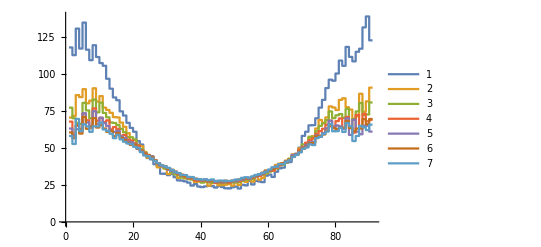

```mathematica
data=Table[Get["Results/NNLODistributions_Matched_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
data2=Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
Abs[(Total/@(data-data2))/(Total/@data2)] 100
ListStepPlot[Join[data,data2],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[Join[{IncRap,exact},IncRap+#&/@(data+data2)],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[#/exact/Total[#]&/@data2,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Total[last]
```

Total::normal: Nonatomic expression expected at position 1 in Total[last].

Total[last]

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

0

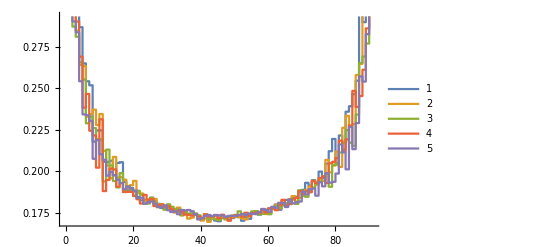

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLO[[;;,2]]),{i,4,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLO[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic]
```

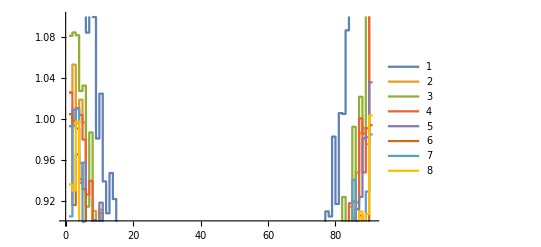

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLOgg[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic,PlotRange->{0.9,1.1}]
```

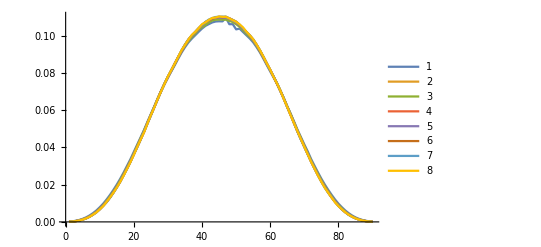

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
ListLinePlot[data,PlotLegends->Automatic,PlotRange->All]
```

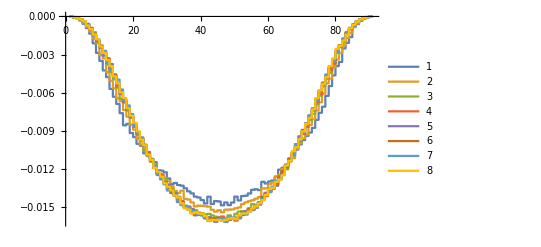

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]),{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

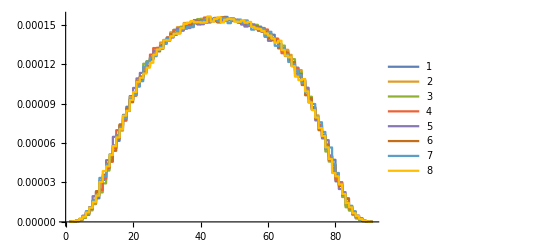

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqqbar[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

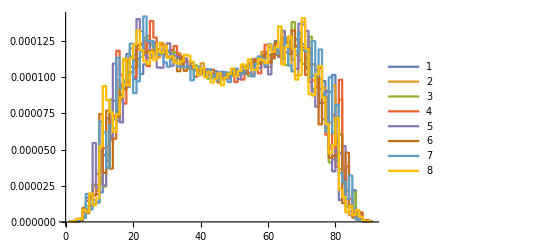

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqq[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

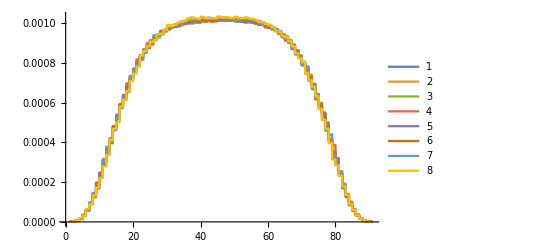

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
RapidityNNLOqQ2[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

## NNLO Distribution

```mathematica
dists=Table[Get["Results/Rapidity/Distributions_"<>StringReplace[ToString[N[i/10]]<>"_125.txt",{"._"->"_"}]];
{i/10//N,Total[RapidityNNLO[[;;,2]]]},{i,0,44}];
```

```mathematica
dists
```

{{0.,9.68177},{0.1,9.67634},{0.2,9.6439},{0.3,9.56922},{0.4,9.471},{0.5,9.35696},{0.6,9.20091},{0.7,9.0193},{0.8,8.82759},{0.9,8.63128},{1.,8.39879},{1.1,8.12811},{1.2,7.81866},{1.3,7.49896},{1.4,7.17656},{1.5,6.84694},{1.6,6.50772},{1.7,6.15035},{1.8,5.77513},{1.9,5.38026},{2.,4.99851},{2.1,4.61609},{2.2,4.21798},{2.3,3.83592},{2.4,3.47121},{2.5,3.11877},{2.6,2.76819},{2.7,2.44039},{2.8,2.12741},{2.9,1.83436},{3.,1.5608},{3.1,1.31049},{3.2,1.08544},{3.3,0.882383},{3.4,0.70238},{3.5,0.546452},{3.6,0.413683},{3.7,0.303867},{3.8,0.21527},{3.9,0.146369},{4.,0.0941393},{4.1,0.056432},{4.2,0.030721},{4.3,0.014362},{4.4,0.0051556}}

```mathematica
Get["XS/Inclusive/InclusiveXS/XS_zb.txt"][[4,5]]/.zb->1-0.642921136448946
```

105.855+1.55228×10^-23 ALARM-118.795 Log[MH2/muf2]+39.5595 Log[MH2/muf2]^2-4.04342 Log[MH2/muf2]^3

```mathematica
Get["Results/NNLOExact1.txt"]
exact=RapidityNNLOqQ2[[;;,2]];
Get["Results/NumericalNNLO.txt"]
numerical=RapidityNNLOgg[[;;,2]];
ListLinePlot[{exact,numerical}]
ListLinePlot[numerical/exact]
```

-Graphics-

-Graphics-

```mathematica
Get["Results/NNLOExact2.txt"]
exact2=RapidityNNLOqQ2[[;;,2]];
Get["Results/NNLOExact3.txt"]
exact3=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[{exact2,exact3}]
ListLinePlot[{exact2/exact,exact3/exact}]
```

-Graphics-

-Graphics-

```mathematica
Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
Total[RapidityNNLOqQ2[[;;,2]]],{i,2,8}]/.fac[0]->1/._fac->1
ListLinePlot[%/Total[exact]]
```

{0.00224539,0.00521604,0.00772705,0.00948283,0.0106268,0.0113691,0.0119371}

-Graphics-

```mathematica
Get["Results/InclusiveNNLOqQ2.txt"];
IncRap=RapidityNNLOqQ2[[;;,2]];
ListLinePlot[IncRap]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Matched_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
data2=Table[Get["Results/NNLODistributions_zb"<>ToString[i]<>".txt"];
RapidityNNLOqQ2[[;;,2]],{i,2,8}]/._fac->1;
Abs[(Total/@(data-data2))/(Total/@data2)] 100
ListStepPlot[Join[data,data2],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[Join[{IncRap,exact},IncRap+#&/@(data+data2)],PlotLegends->Automatic,PlotRange->All]
ListStepPlot[#/exact/Total[#]&/@data2,PlotLegends->Automatic,PlotRange->All]
```

{200.23,199.191,199.993,199.975,199.904,199.919,199.977}

-Graphics-

-Graphics-

-Graphics-

```mathematica
Total[last]
```

7.83301

```mathematica
RapidityNNLOgg[[;;,2]]//Total
```

10.9369

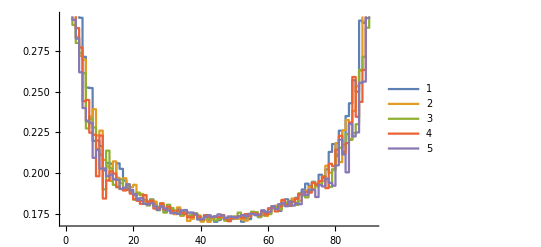

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLO[[;;,2]]),{i,4,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLO[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic]
```

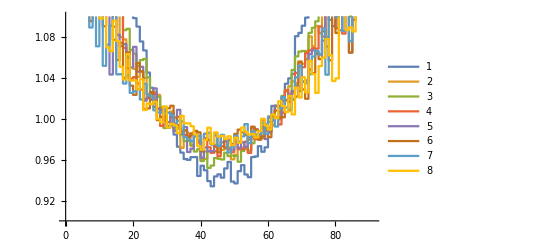

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
Get["Results/NumericalNNLO.txt"]
last=RapidityNNLOgg[[;;,2]];
ListStepPlot[#/last&/@data,PlotLegends->Automatic,PlotRange->{0.9,1.1}]
```

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
(RapidityNNLOgg[[;;,2]]),{i,1,8}]/._fac->1;
ListLinePlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
(RapidityNNLOqg[[;;,2]]+RapidityNNLOgq[[;;,2]]),{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqqbar[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>".txt"];
RapidityNNLOqq[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data=Table[Get["Results/NNLODistributions_Subtracted_zb"<>ToString[i]<>"_625.txt"];
RapidityNNLOqQ2[[;;,2]],{i,1,8}]/._fac->1;
ListStepPlot[data,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

## N3LO Rapidity

```mathematica
GetDistribution[order_,zb_,scale_]:=Block[{dist},dist=Table[Get["Results/Rapidity/Distributions_N3LO_Y"<>StringReplace[ToString[N[i/10]]<>"_mu"<>ToString[scale]<>"_zb"<>ToString[zb]<>".txt",{"._"->"_"}]];
{i/10//N,Total[ToExpression["Rapidity"<>ToString[order]][[;;,2]]]},{i,0,44}];
dist=DeleteDuplicates[Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]];
Return[dist];
];
```

```mathematica
Dist125=GetDistribution[LO,6,125];
Dist625=GetDistribution[LO,6,62.5];
Dist3125=GetDistribution[LO,6,31.25];
Dist42=GetDistribution[LO,6,42];
LOMax=Table[{Dist125[[i,1]],Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
LOMin=Table[{Dist125[[i,1]],Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
LOCent=Table[{Dist625[[i,1]],Dist625[[i,2]]},{i,1,Length[Dist125]}];
Export["Results/Rapidity_LO.m",{{125,Dist125},{62.5,Dist625},{31.25,Dist3125},{42,Dist42}}];
```

```mathematica
Dist125=GetDistribution[NLO,6,125];
Dist625=GetDistribution[NLO,6,62.5];
Dist3125=GetDistribution[NLO,6,31.25];
Dist42=GetDistribution[NLO,6,42];
NLOMax=Table[{Dist125[[i,1]],Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
NLOMin=Table[{Dist125[[i,1]],Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
NLOCent=Table[{Dist625[[i,1]],Dist625[[i,2]]},{i,1,Length[Dist125]}];
Export["Results/Rapidity_NLO.m",{{125,Dist125},{62.5,Dist625},{31.25,Dist3125},{42,Dist42}}];
```

```mathematica
Dist125=GetDistribution[NNLO,6,125];
Dist625=GetDistribution[NNLO,6,62.5];
Dist3125=GetDistribution[NNLO,6,31.25];
Dist42=GetDistribution[NNLO,6,42];
NNLOMax=Table[{Dist125[[i,1]],Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
NNLOMin=Table[{Dist125[[i,1]],Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
NNLOCent=Table[{Dist625[[i,1]],Dist625[[i,2]]},{i,1,Length[Dist125]}];
Export["Results/Rapidity_NNLO.m",{{125,Dist125},{62.5,Dist625},{31.25,Dist3125},{42,Dist42}}];
```

```mathematica
Dist125=GetDistribution[N3LO,6,125];
Dist625=GetDistribution[N3LO,6,62.5];
Dist3125=GetDistribution[N3LO,6,31.25];
Dist42=GetDistribution[N3LO,6,42];
N3LOMax=Table[{Dist125[[i,1]],Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
N3LOMin=Table[{Dist125[[i,1]],Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]},{i,1,Length[Dist125]}];
N3LOCent=Table[{Dist625[[i,1]],Dist625[[i,2]]},{i,1,Length[Dist125]}];
Export["Results/Rapidity_N3LO.m",{{125,Dist125},{62.5,Dist625},{31.25,Dist3125},{42,Dist42}}];
```

```mathematica
dists={LOCent,NLOCent,NNLOCent,N3LOCent,LOMax,LOMin,NLOMax,NLOMin,NNLOMax,NNLOMin,N3LOMax,N3LOMin};
```

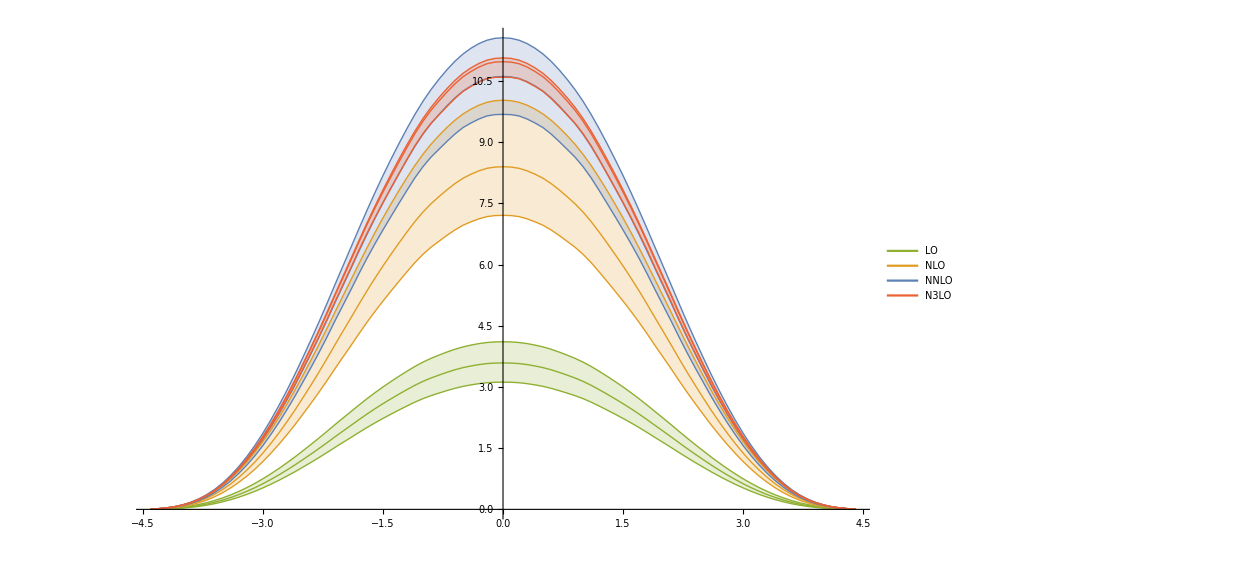

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]],Thin},
{ColorData[97,"ColorList"][[4]],Thin}
},
Filling->{5->{1},6->{1},7->{2},8->{2},9->{3},10->{3},11->{4},12->{4}},
PlotLegends->Placed[LineLegend[{"LO\t     ","NLO\t","NNLO\t","N3LO\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.8}]
]
```

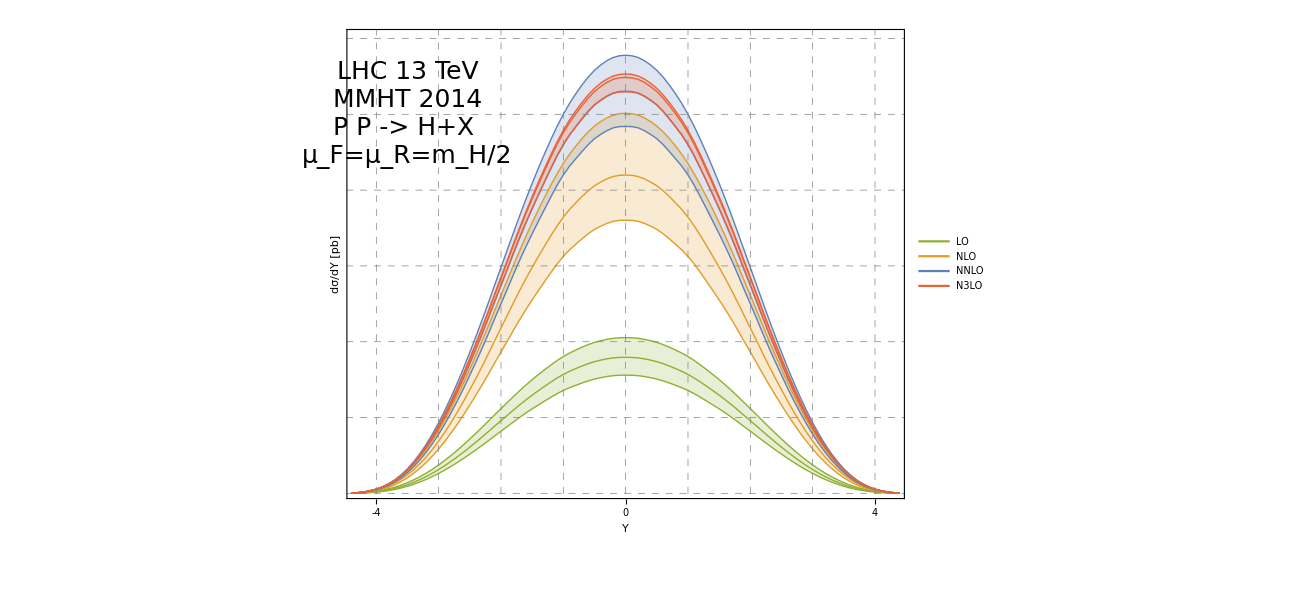

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.1,12}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],2Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[2i,{i,-10,12}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ/dY [pb]"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3.5,10}]
]
```

## N3LO Rapidity - Normalised to NNLO

```mathematica
GetDistribution[order_,zb_,scale_]:=Block[{dist},dist=Table[Get["Results/Rapidity/Distributions_N3LO_Y"<>StringReplace[ToString[N[i/10]]<>"_mu"<>ToString[scale]<>"_zb"<>ToString[zb]<>".txt",{"._"->"_"}]];
{i/10//N,Total[ToExpression["Rapidity"<>ToString[order]][[;;,2]]]},{i,0,44}];
dist=DeleteDuplicates[Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]];
Return[dist];
];
```

```mathematica
Dist125=GetDistribution[NNLO,6,125];
Dist625=GetDistribution[NNLO,6,62.5];
Dist3125=GetDistribution[NNLO,6,31.25];
Dist42=GetDistribution[NNLO,6,42];
NNLOCent=Table[Dist625[[i,2]],{i,1,Length[Dist125]}];
NNLOMax=Table[Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]/NNLOCent[[i]],{i,1,Length[Dist125]}];
NNLOMin=Table[Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]/NNLOCent[[i]],{i,1,Length[Dist125]}];
```

```mathematica
Dist125=GetDistribution[N3LO,6,125];
Dist625=GetDistribution[N3LO,6,62.5];
Dist3125=GetDistribution[N3LO,6,31.25];
Dist42=GetDistribution[N3LO,6,42];
N3LOMax=Table[Max[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]/NNLOCent[[i]],{i,1,Length[Dist125]}];
N3LOMin=Table[Min[{Dist125[[i,2]],Dist625[[i,2]],Dist3125[[i,2]],Dist42[[i,2]]}]/NNLOCent[[i]],{i,1,Length[Dist125]}];
N3LOCent=Table[Dist625[[i,2]]/NNLOCent[[i]],{i,1,Length[Dist125]}];
```

```mathematica
NNLOCent2=Table[1,{i,1,Length[NNLOCent]}];
xrange=Dist125[[;;,1]]
```

{-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4}

```mathematica
dists={NNLOCent2,N3LOCent,NNLOMax,NNLOMin,N3LOMax,N3LOMin};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

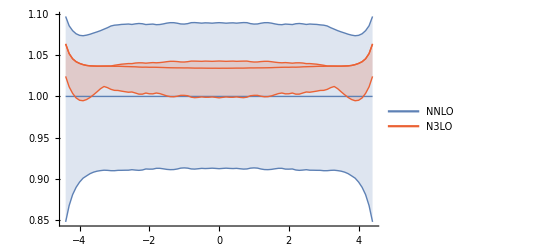

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]],Thin},
{ColorData[97,"ColorList"][[4]],Thin}
},
Filling->{3->{1},4->{1},5->{2},6->{2},9->{3},10->{3},11->{4},12->{4}},
PlotLegends->Placed[LineLegend[{"NNLO\t","N3LO\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.2}],
PlotRange->All
]
```

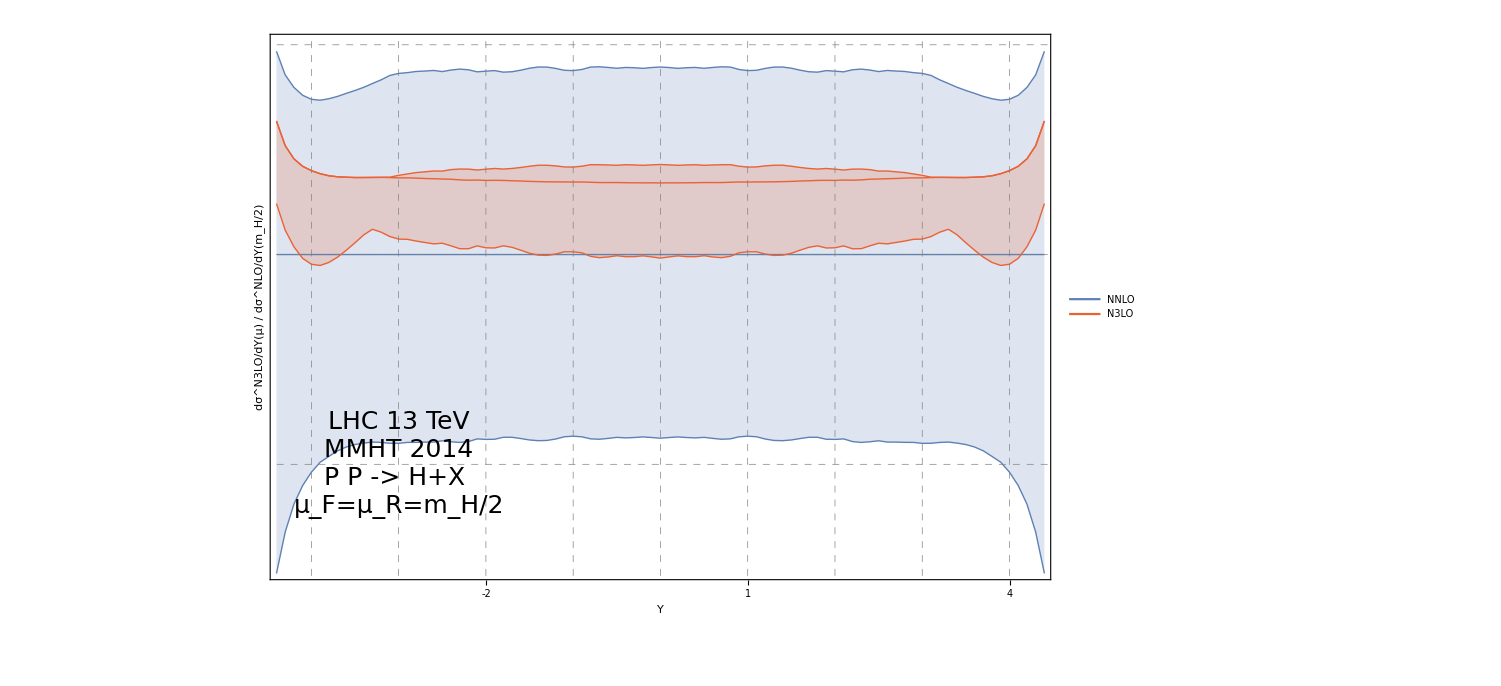

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.85,1.1}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,12}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^N3LO/dY(μ) / dσ^NLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3,0.9}]
]
```

## NNLO Rapidity Threshold Expansion

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

```mathematica
GetDistribution[file_,scale_,order_,zb_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
file=NNLOExp;
```

```mathematica
scale=125;
```

```mathematica
xrange=GetDistribution[NNLO,scale,NNLO][[;;,1]];
```

```mathematica
norm=GetDistribution[NNLO,scale,NNLO][[;;,2]];
```

```mathematica
NNLO2=GetDistribution[file,scale,NNLO,2][[;;,2]]/norm;
NNLO3=GetDistribution[file,scale,NNLO,3][[;;,2]]/norm;
NNLO4=GetDistribution[file,scale,NNLO,4][[;;,2]]/norm;
NNLO5=GetDistribution[file,scale,NNLO,5][[;;,2]]/norm;
NNLO6=GetDistribution[file,scale,NNLO,6][[;;,2]]/norm;
NNLO7=GetDistribution[file,scale,NNLO,7][[;;,2]]/norm;
NNLO8=GetDistribution[file,scale,NNLO,8][[;;,2]]/norm;
```

```mathematica
dists={NNLO2,NNLO3,NNLO4,NNLO5,NNLO6,norm/norm,NNLO7,NNLO8};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

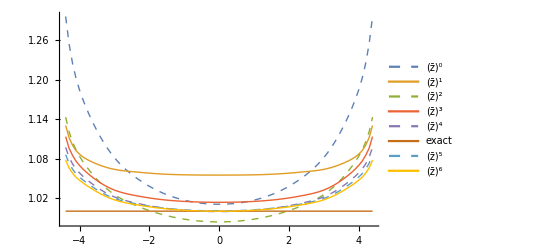

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick,Dashed},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick,Dashed},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[5]],Thick,Dashed},
{ColorData[97,"ColorList"][[6]],Thick},
{ColorData[97,"ColorList"][[7]],Thick,Dashed},
{ColorData[97,"ColorList"][[8]],Thick}
},
PlotLegends->Placed[LineLegend[{"(z̄)^0\t","(z̄)^1\t","(z̄)^2\t","(z̄)^3\t","(z̄)^4\t","exact","(z̄)^5\t","(z̄)^6\t"},LegendLayout->{"Row",4},LabelStyle->20],{0.85,0.2}],
PlotRange->All
]
```

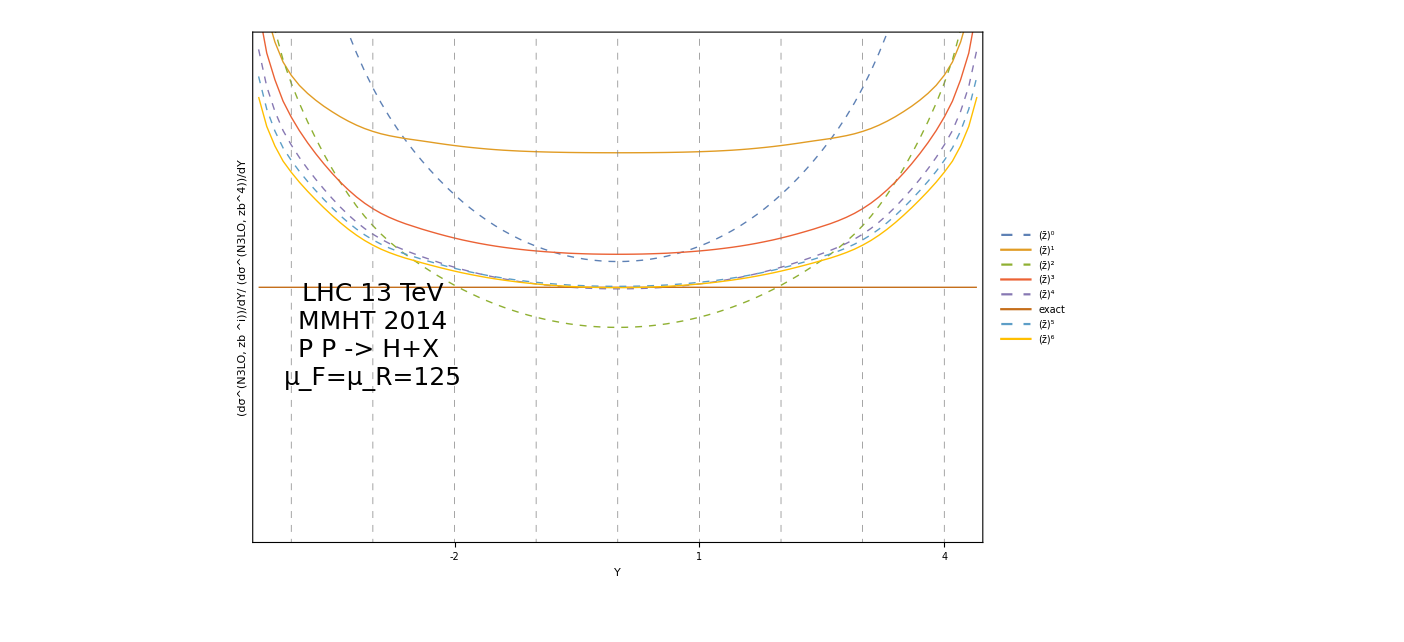

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.90,1.1}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.01Table[{i,i},{i,-50,120}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.01i,{i,-10,120}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","(dσ^(N3LO, zb ^i))/dY/ (dσ^(N3LO,  zb^4))/dY"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=125",25,TextAlignment->Left],{-3,0.98}]
]
```

## NNLO Rapidity Threshold Expansion Reweighted

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

```mathematica
GetDistribution[file_,scale_,order_,zb_]:=
Block[{i,j,k,dist,max,exact,approx,ratio},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
exact=ToExpression[StringReplace[Import["Results/Rapidity/CrossSection_"<>StringReplace[ToString[order]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[;;,1]];
approx=ToExpression[StringReplace[Import["Results/Rapidity/CrossSection_"<>StringReplace[ToString[file]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[;;,1]];
ratio=Table[If[!MatchQ[approx[[i]],0],exact[[i]]/approx[[i]],1],{i,1,Length[exact]}];
dist=Table[
{N[i/10], ratio[[max]].ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
file=NNLOExpRegular;
```

```mathematica
scale=125;
```

```mathematica
xrange=GetDistribution[NNLO,scale,NNLO][[;;,1]];
```

```mathematica
norm=GetDistribution[NNLO,scale,NNLO][[;;,2]];
```

```mathematica
NNLO2=GetDistribution[file,scale,NNLO,2][[;;,2]]/norm;
NNLO3=GetDistribution[file,scale,NNLO,3][[;;,2]]/norm;
NNLO4=GetDistribution[file,scale,NNLO,4][[;;,2]]/norm;
NNLO5=GetDistribution[file,scale,NNLO,5][[;;,2]]/norm;
NNLO6=GetDistribution[file,scale,NNLO,6][[;;,2]]/norm;
NNLO7=GetDistribution[file,scale,NNLO,7][[;;,2]]/norm;
NNLO8=GetDistribution[file,scale,NNLO,8][[;;,2]]/norm;
```

```mathematica
dists={NNLO2,NNLO3,NNLO4,NNLO5,NNLO6,norm/norm,NNLO7,NNLO8};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

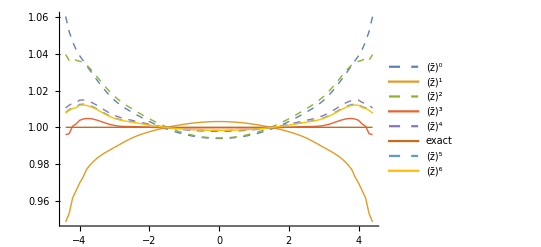

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick,Dashed},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick,Dashed},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[5]],Thick,Dashed},
{ColorData[97,"ColorList"][[6]],Thick},
{ColorData[97,"ColorList"][[7]],Thick,Dashed},
{ColorData[97,"ColorList"][[8]],Thick}
},
PlotLegends->Placed[LineLegend[{"(z̄)^0\t","(z̄)^1\t","(z̄)^2\t","(z̄)^3\t","(z̄)^4\t","exact","(z̄)^5\t","(z̄)^6\t"},LegendLayout->{"Row",4},LabelStyle->20],{0.85,0.2}],
PlotRange->All
]
```

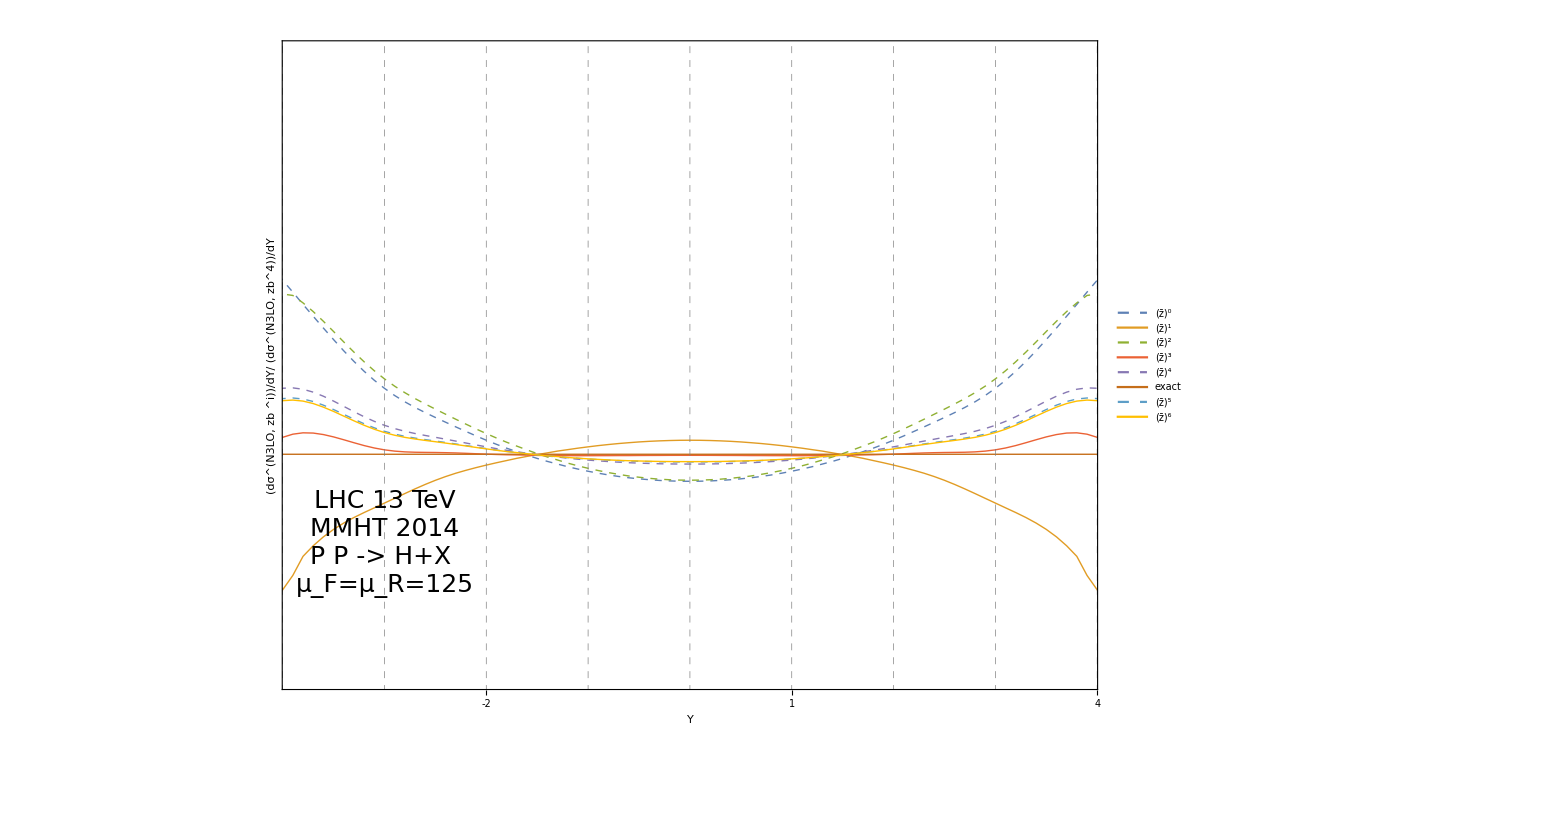

```mathematica
ppp=Show[pp,
PlotRange->{{-3.85,3.85},{0.95,1.09}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.01Table[{i,i},{i,-50,120}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.01i,{i,-10,120}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","(dσ^(N3LO, zb ^i))/dY/ (dσ^(N3LO,  zb^4))/dY"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=125",25,TextAlignment->Left],{-3,0.98}]
]
```

## N3LO Rapidity Threshold Expansion

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

```mathematica
GetDistribution[file_,scale_,order_,zb_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
file=N3LOExp;
```

```mathematica
scale=125;
```

```mathematica
xrange=GetDistribution[NNLO,scale,NNLO][[;;,1]];
```

```mathematica
norm=1.1  GetDistribution[NNLO,scale,NNLO][[;;,2]];
```

```mathematica
GetDistribution[file,scale,N3LO,6][[45;;]]
```

{{0.,10.6456},{0.1,10.631},{0.2,10.5869},{0.3,10.5135},{0.4,10.4108},{0.5,10.2792},{0.6,10.1187},{0.7,9.93072},{0.8,9.71539},{0.9,9.47391},{1.,9.20728},{1.1,8.9164},{1.2,8.60253},{1.3,8.26727},{1.4,7.91237},{1.5,7.53994},{1.6,7.15202},{1.7,6.75147},{1.8,6.34127},{1.9,5.92422},{2.,5.50324},{2.1,5.08125},{2.2,4.66125},{2.3,4.24655},{2.4,3.84033},{2.5,3.44564},{2.6,3.06522},{2.7,2.70156},{2.8,2.35707},{2.9,2.0337},{3.,1.73297},{3.1,1.45632},{3.2,1.20495},{3.3,0.979678},{3.4,0.780974},{3.5,0.608841},{3.6,0.462526},{3.7,0.341032},{3.8,0.242642},{3.9,0.16559},{4.,0.107197},{4.1,0.0648099},{4.2,0.0356221},{4.3,0.0169344},{4.4,0.0062377}}

```mathematica
NNLO2=GetDistribution[file,scale,N3LO,2][[;;,2]]/norm;
NNLO3=GetDistribution[file,scale,N3LO,3][[;;,2]]/norm;
NNLO4=GetDistribution[file,scale,N3LO,4][[;;,2]]/norm;
NNLO5=GetDistribution[file,scale,N3LO,5][[;;,2]]/norm;
NNLO6=GetDistribution[file,scale,N3LO,6][[;;,2]]/norm;
```

```mathematica
dists={NNLO2,NNLO3,NNLO4,NNLO5,NNLO6,norm/norm};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

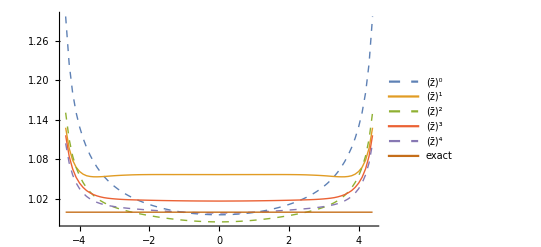

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick,Dashed},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick,Dashed},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[5]],Thick,Dashed},
{ColorData[97,"ColorList"][[6]],Thick}
},
PlotLegends->Placed[LineLegend[{"(z̄)^0\t","(z̄)^1\t","(z̄)^2\t","(z̄)^3\t","(z̄)^4\t","exact"},LegendLayout->{"Row",3},LabelStyle->20],{0.85,0.2}],
PlotRange->All
]
```

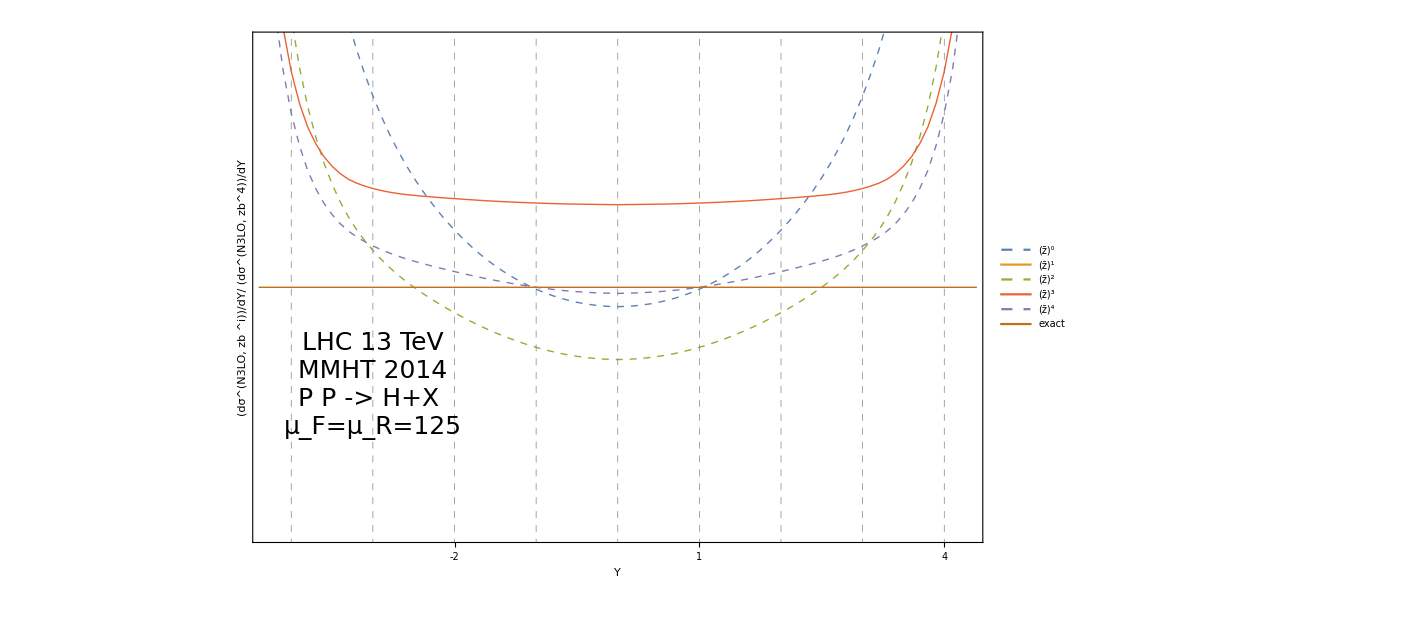

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.95,1.05}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.01Table[{i,i},{i,-50,120}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.01i,{i,-10,120}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","(dσ^(N3LO, zb ^i))/dY/ (dσ^(N3LO,  zb^4))/dY"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=125",25,TextAlignment->Left],{-3,0.98}]
]
```

## N3LO Rapidity Threshold Expansion

```mathematica
GetDistribution[order_,zb_,scale_]:=Block[{dist},dist=Table[Get["Results/Rapidity/Distributions_N3LO_Y"<>StringReplace[ToString[N[i/10]]<>"_mu"<>ToString[scale]<>"_zb"<>ToString[zb]<>".txt",{"._"->"_"}]];
{i/10//N,Total[ToExpression["Rapidity"<>ToString[order]][[;;,2]]]},{i,0,44}];
dist=DeleteDuplicates[Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]];
Return[dist];
];
```

```mathematica
Dist125=GetDistribution[NNLO,6,125];
NNLODist=Dist125[[;;,2]];
```

```mathematica
xrange=Dist125[[;;,1]];
```

```mathematica
norm=GetDistribution[N3LO,6,125][[;;,2]];
```

```mathematica
N3LO2=GetDistribution[N3LO,2,125][[;;,2]]/norm;
N3LO3=GetDistribution[N3LO,3,125][[;;,2]]/norm;
N3LO4=GetDistribution[N3LO,4,125][[;;,2]]/norm;
N3LO5=GetDistribution[N3LO,5,125][[;;,2]]/norm;
N3LO6=GetDistribution[N3LO,6,125][[;;,2]]/norm;
```

```mathematica
dists={N3LO2,N3LO3,N3LO4,N3LO5,N3LO6};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

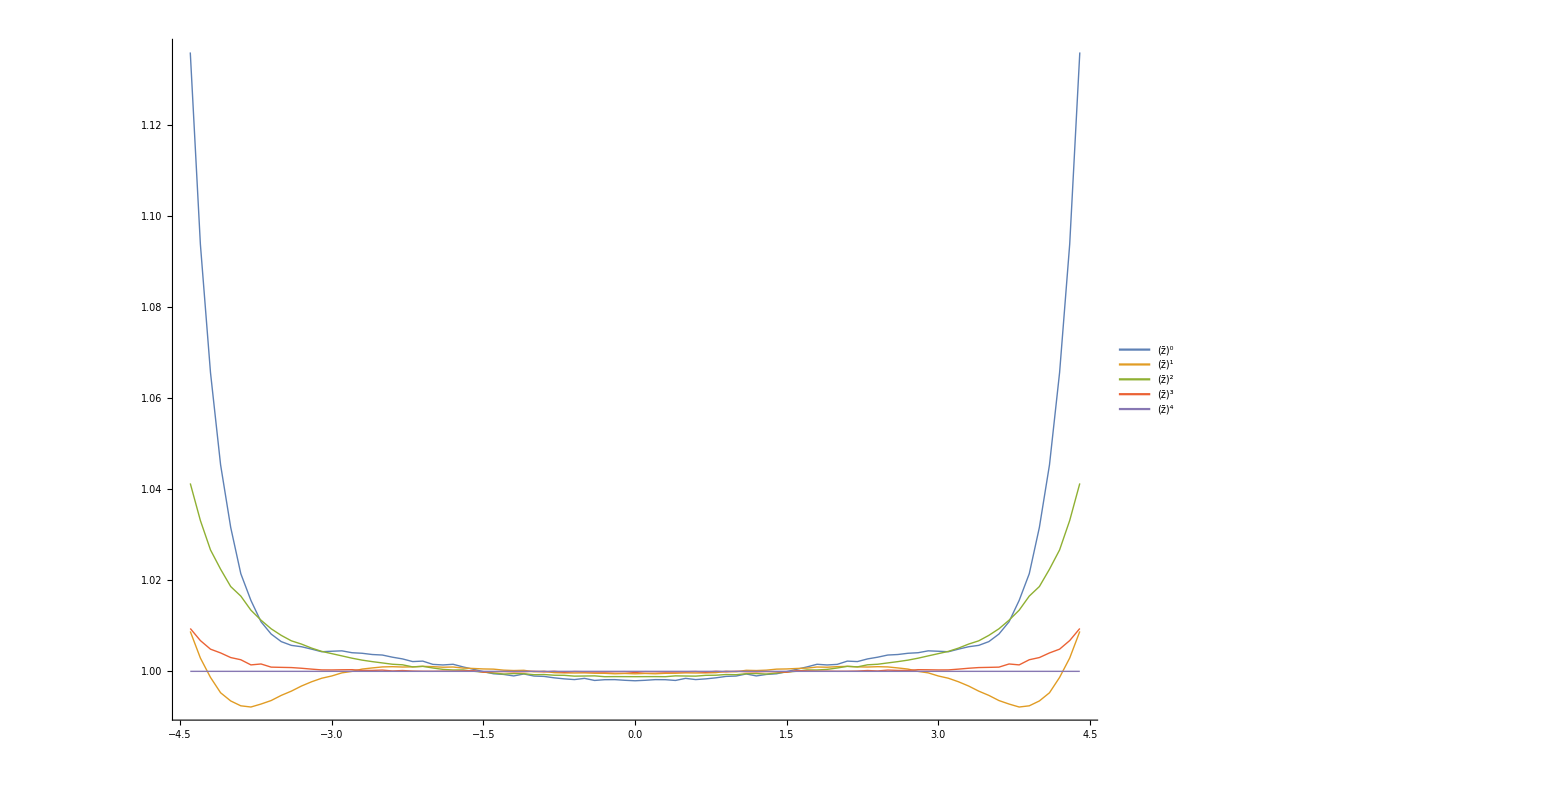

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[5]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"(z̄)^0\t","(z̄)^1\t","(z̄)^2\t","(z̄)^3\t","(z̄)^4\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.2}],
PlotRange->All
]
```

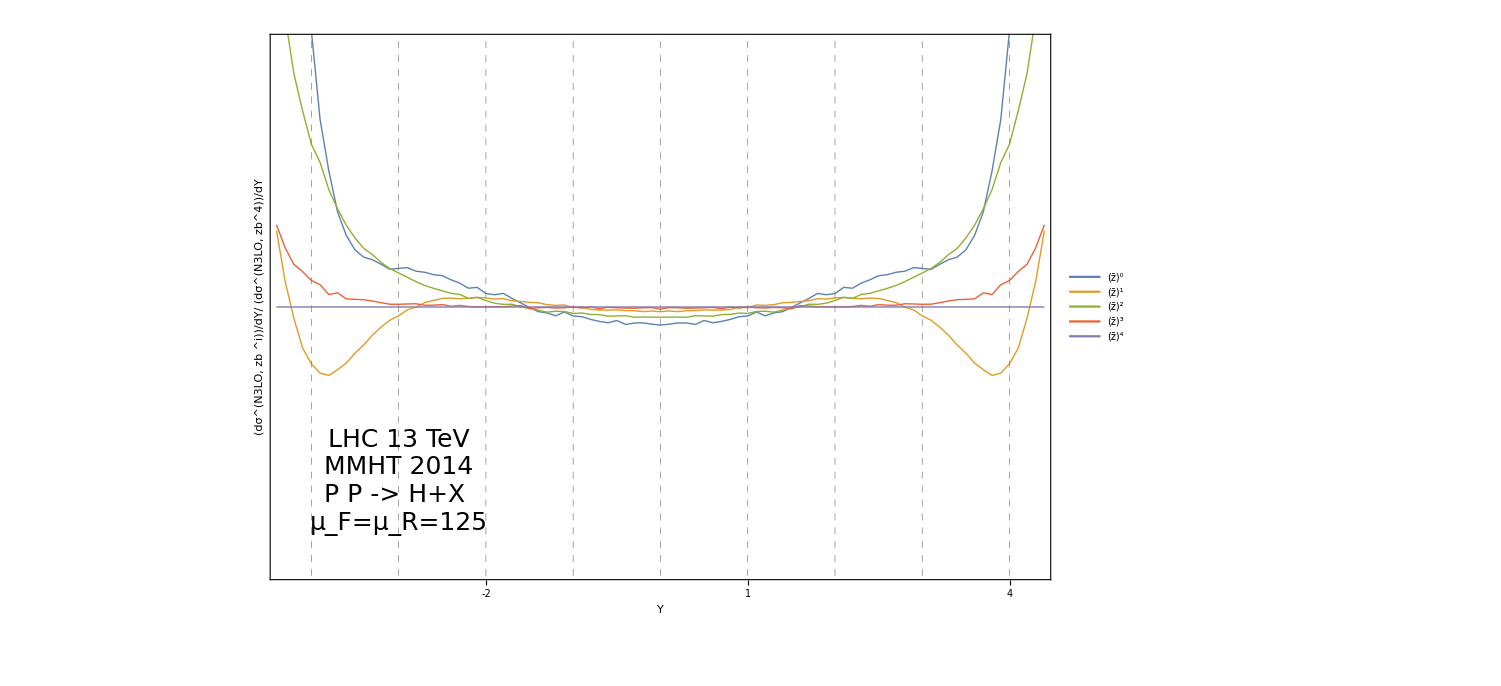

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.97,1.03}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.01Table[{i,i},{i,-50,120}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.01i,{i,-10,120}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","(dσ^(N3LO, zb ^i))/dY/ (dσ^(N3LO,  zb^4))/dY"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=125",25,TextAlignment->Left],{-3,0.98}]
]
```

## N3LO Rapidity Threshold Expansion Unmatched

```mathematica
GetDistribution[order_,zb_,scale_]:=Block[{dist},dist=Table[Get["Results/Rapidity/Distributions_N3LO_Unmatched_Y"<>StringReplace[ToString[N[i/10]]<>"_mu"<>ToString[scale]<>"_zb"<>ToString[zb]<>".txt",{"._"->"_"}]];
{i/10//N,Total[ToExpression["Rapidity"<>ToString[order]][[;;,2]]]},{i,0,44}];
dist=DeleteDuplicates[Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]];
Return[dist];
];
```

```mathematica
Dist125=GetDistribution[NNLO,6,125];
NNLODist=Dist125[[;;,2]];
```

```mathematica
xrange=Dist125[[;;,1]];
```

```mathematica
norm=GetDistribution[N3LO,6,125][[;;,2]];
```

```mathematica
N3LO2=GetDistribution[N3LO,2,125][[;;,2]]/norm;
N3LO3=GetDistribution[N3LO,3,125][[;;,2]]/norm;
N3LO4=GetDistribution[N3LO,4,125][[;;,2]]/norm;
N3LO5=GetDistribution[N3LO,5,125][[;;,2]]/norm;
N3LO6=GetDistribution[N3LO,6,125][[;;,2]]/norm;
```

```mathematica
dists={N3LO2,N3LO3,N3LO4,N3LO5,N3LO6};
dists=Table[Table[{xrange[[j]],dists[[i,j]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

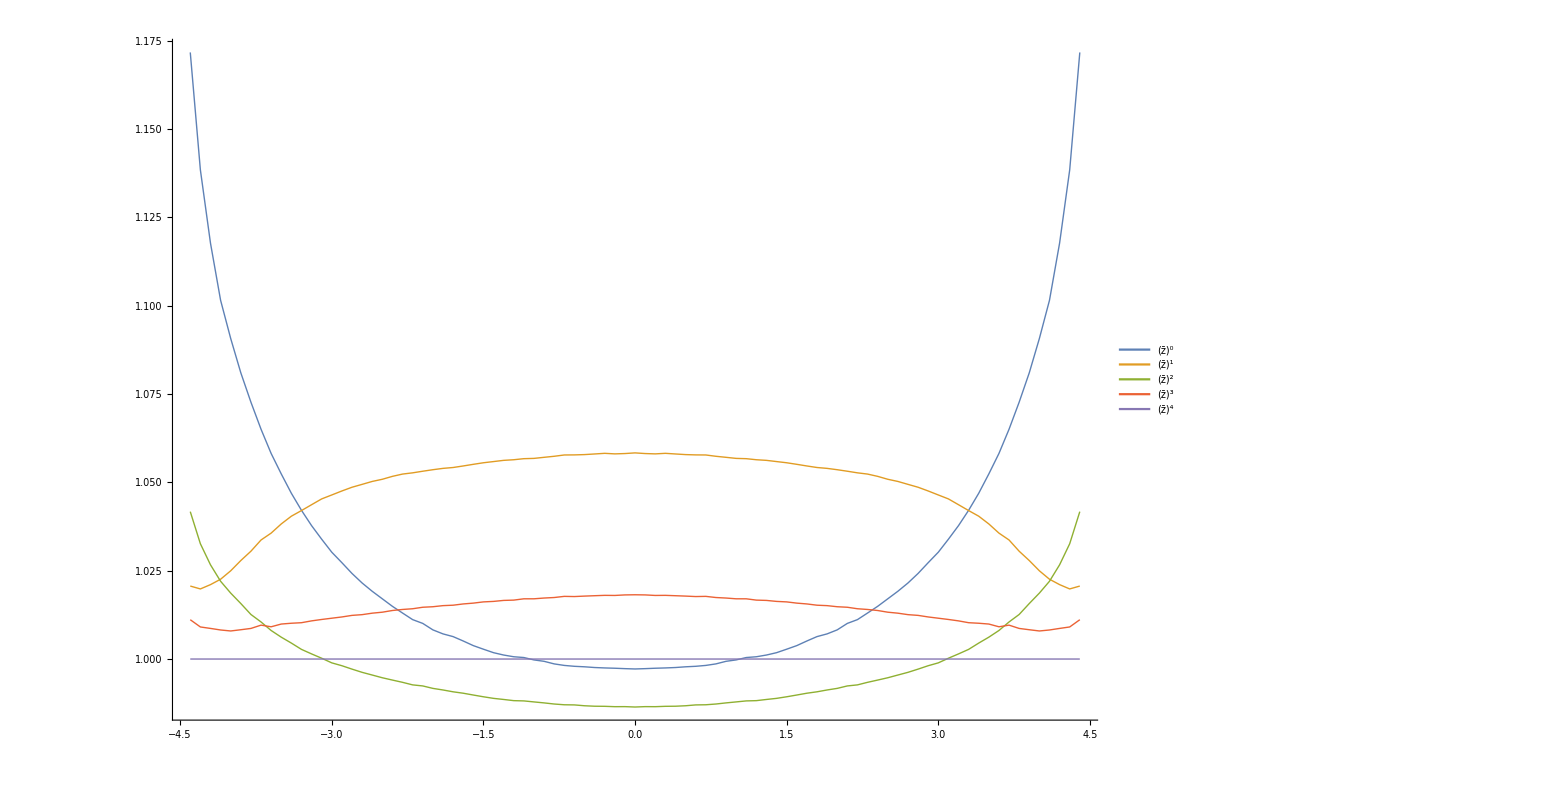

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[5]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"(z̄)^0\t","(z̄)^1\t","(z̄)^2\t","(z̄)^3\t","(z̄)^4\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.2}],
PlotRange->All
]
```

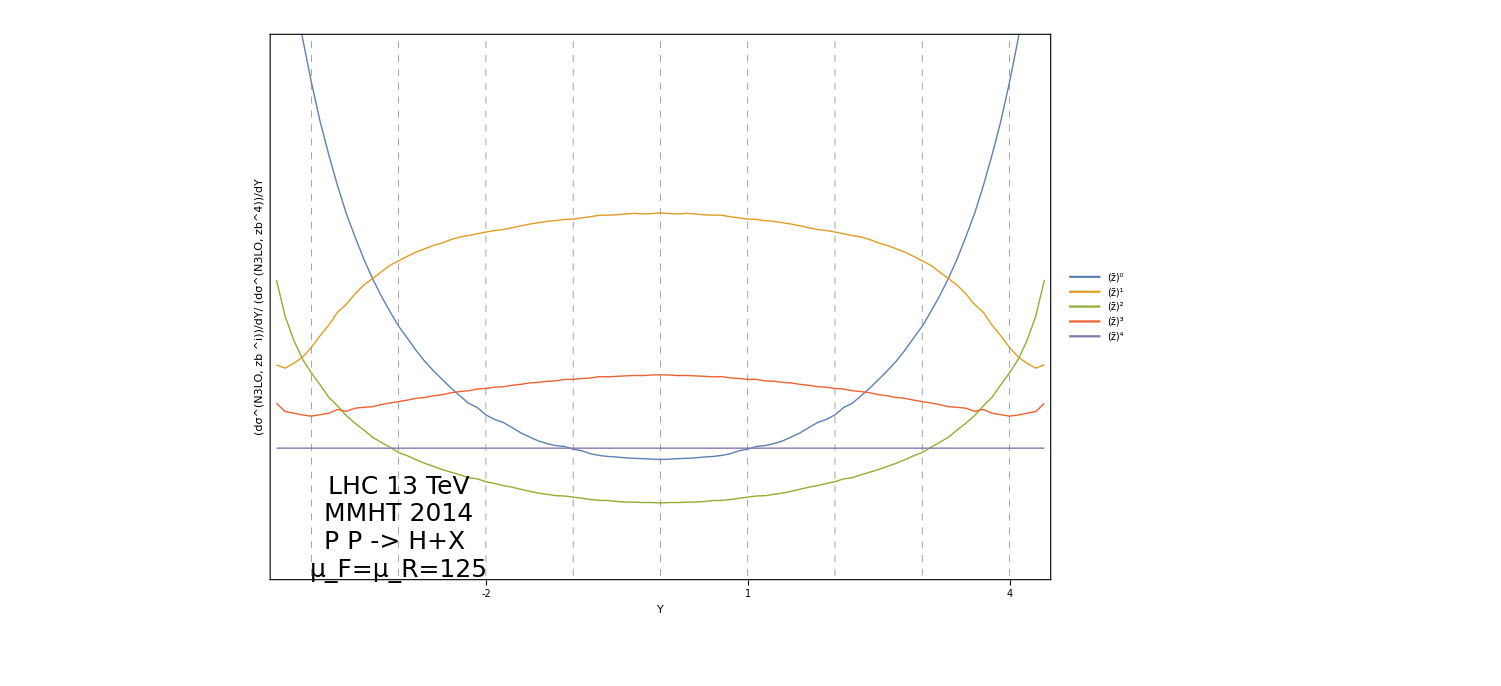

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.97,1.10}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.01Table[{i,i},{i,-50,120}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.01i,{i,-10,120}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","(dσ^(N3LO, zb ^i))/dY/ (dσ^(N3LO,  zb^4))/dY"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=125",25,TextAlignment->Left],{-3,0.98}]
]
```

## N3LO Matched but with LHAPDF directly

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

```mathematica
GetDistribution[file_,scale_,order_,zb_]:=
Block[{i,j,k,dist,max,exact,approx,ratio},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
exact=ToExpression[StringReplace[Import["Results/Rapidity/CrossSection_"<>StringReplace[ToString[order]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[;;,1]];
approx=ToExpression[StringReplace[Import["Results/Rapidity/CrossSection_"<>StringReplace[ToString[file]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[;;,1]];
ratio=Table[If[!MatchQ[approx[[i]],0],exact[[i]]/approx[[i]],1],{i,1,Length[exact]}];
dist=Table[
{N[i/10], ratio[[max]].ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zb]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
res=Table[Import["Results/Rapidity/RapidityNoGrid_NNLO_Y"<>StringReplace[ToString[N[i/10]]<>"_mu125.txt",{"._"->"_"}]],{i,0,45}];
```

```mathematica
Position[res,$Failed]
```

{}

```mathematica
res2=ToExpression[StringReplace[#,"e-"->"*10^-"]]&/@Select[res,!MatchQ[#,$Failed]&];
```

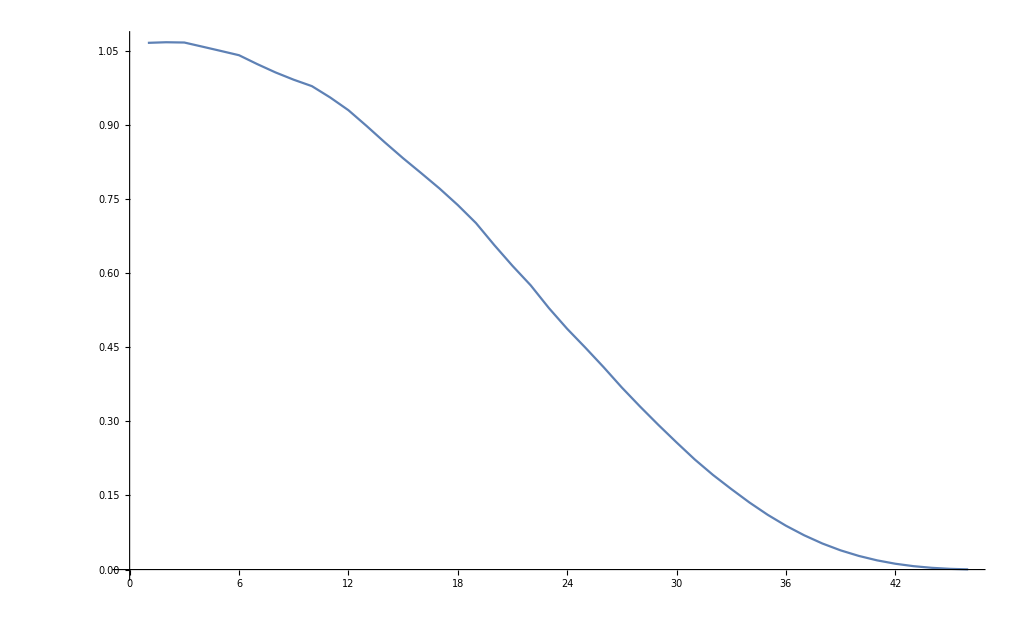

```mathematica
ListLinePlot[res2[[;;,4,1]]]
```